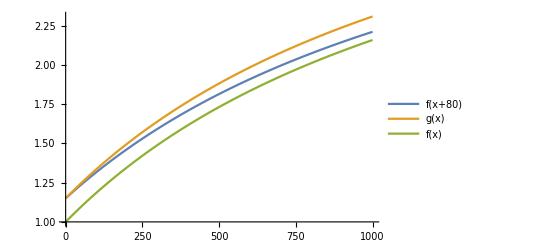

1.46333

1.4975

1.02335

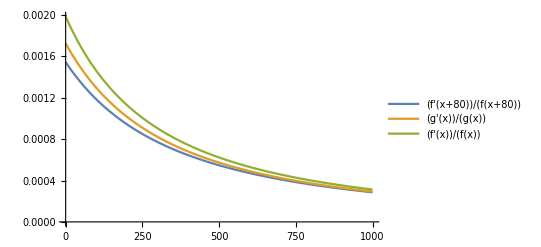

```mathematica
f[x_]:=2.78x/(1400+x)+1
g[x_]:=2.78x/(1400+x)+1.15
Plot[{f[x+80],g[x],f[x]},{x,0,1000},AxesOrigin->{0,1},PlotLegends->"Expressions"]
f[200+80]
g[200]
g[200]/f[200+80]
Plot[{f'[x+80]/f[x+80],g'[x]/g[x],f'[x]/f[x]},{x,0,1000},AxesOrigin->{0,0},PlotLegends->"Expressions"]
```

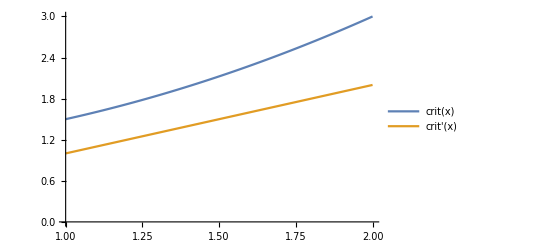

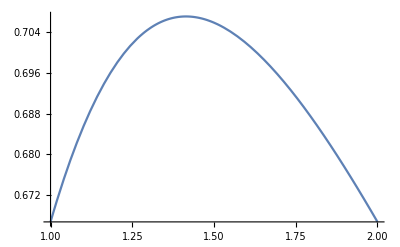

```mathematica
crit[x_]:=1+0.5x^2
Plot[{crit[x],crit'[x]},{x,1,2},AxesOrigin->{1,0},PlotLegends->"Expressions"]
Plot[{crit'[x]/crit[x]},{x,1,2},PlotLegends->"Expressions"]
```

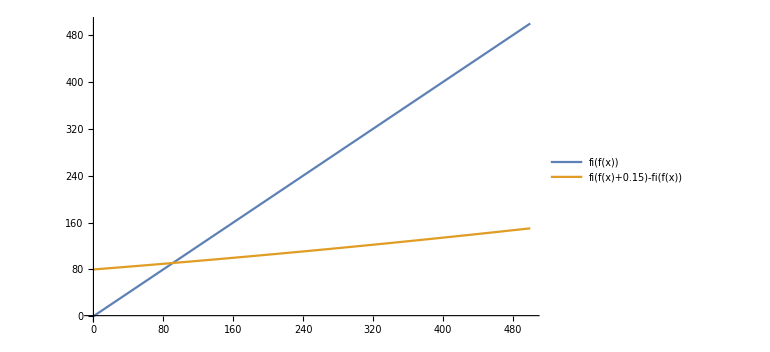

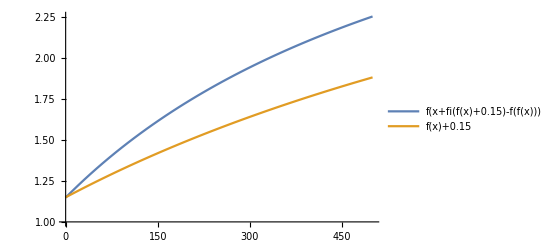

```mathematica
fi[y_]:=1400(y-1)/(2.78-(y-1))
Plot[{fi[f[x]],fi[f[x]+0.15]-fi[f[x]]},{x,0,500},AxesOrigin->{0,1},PlotLegends->"Expressions"]
Plot[{f[x+fi[f[x]+0.15]-f[f[x]]],f[x]+0.15},{x,0,500},AxesOrigin->{0,1},PlotLegends->"Expressions"]
```